```mathematica
munten = 47*0.89+6
```

47.83

```mathematica
balls1= {27,26.8,26.5,25.9,25.7,25.2,24.9,24.5,23.9,23.5,23.0,22.8,22.6,22.5,22.5}
```

{27,26.8,26.5,25.9,25.7,25.2,24.9,24.5,23.9,23.5,23.,22.8,22.6,22.5,22.5}

```mathematica
data = Table[{47+(i-1)*2,balls1[[i]]},{i,1,Length[balls1]}]
```

{{47,27},{49,26.8},{51,26.5},{53,25.9},{55,25.7},{57,25.2},{59,24.9},{61,24.5},{63,23.9},{65,23.5},{67,23.},{69,22.8},{71,22.6},{73,22.5},{75,22.5}}

```mathematica
(**4 Kugeln **)
balls2 = {22.3,22.2,22.0,21.9,21.8,21.5,21.4,21.3,21.2,21.1,20.8,20.7,20.6,20.4,20.2,20.2,20.0}
```

{22.3,22.2,22.,21.9,21.8,21.5,21.4,21.3,21.2,21.1,20.8,20.7,20.6,20.4,20.2,20.2,20.}

```mathematica
Append[data,Table[{75+i*4,balls2[[i]]},{i,1,Length[balls2]}]]
```

```mathematica
data = {{47,27},{49,26.8},{51,26.5},{53,25.9},{55,25.7},{57,25.2},{59,24.9},{61,24.5},{63,23.9},{65,23.5},{67,23.},{69,22.8},{71,22.6},{73,22.5},{75,22.5},{79,22.3},{83,22.2},{87,22.},{91,21.9},{95,21.8},{99,21.5},{103,21.4},{107,21.3},{111,21.2},{115,21.1},{119,20.8},{123,20.7},{127,20.6},{131,20.4},{135,20.2},{139,20.2},{143,20.}}
```

{{47,27},{49,26.8},{51,26.5},{53,25.9},{55,25.7},{57,25.2},{59,24.9},{61,24.5},{63,23.9},{65,23.5},{67,23.},{69,22.8},{71,22.6},{73,22.5},{75,22.5},{79,22.3},{83,22.2},{87,22.},{91,21.9},{95,21.8},{99,21.5},{103,21.4},{107,21.3},{111,21.2},{115,21.1},{119,20.8},{123,20.7},{127,20.6},{131,20.4},{135,20.2},{139,20.2},{143,20.}}

```mathematica
(**7 Kugeln**)
```

```mathematica
balls3 ={19.8,19.1,18.8,18.5,18.4,18.1}
```

{19.8,19.1,18.8,18.5,18.4,18.1}

```mathematica
AppendTo[data,Table[{143+i*7,balls3[[i]]},{i,1,Length[balls3]}]]
```

```mathematica
data = {{47,27},{49,26.8},{51,26.5},{53,25.9},{55,25.7},{57,25.2},{59,24.9},{61,24.5},{63,23.9},{65,23.5},{67,23.},{69,22.8},{71,22.6},{73,22.5},{75,22.5},{79,22.3},{83,22.2},{87,22.},{91,21.9},{95,21.8},{99,21.5},{103,21.4},{107,21.3},{111,21.2},{115,21.1},{119,20.8},{123,20.7},{127,20.6},{131,20.4},{135,20.2},{139,20.2},{143,20.},{150,19.8},{157,19.1},{164,18.8},{171,18.5},{178,18.4},{185,18.1}}
```

{{47,27},{49,26.8},{51,26.5},{53,25.9},{55,25.7},{57,25.2},{59,24.9},{61,24.5},{63,23.9},{65,23.5},{67,23.},{69,22.8},{71,22.6},{73,22.5},{75,22.5},{79,22.3},{83,22.2},{87,22.},{91,21.9},{95,21.8},{99,21.5},{103,21.4},{107,21.3},{111,21.2},{115,21.1},{119,20.8},{123,20.7},{127,20.6},{131,20.4},{135,20.2},{139,20.2},{143,20.},{150,19.8},{157,19.1},{164,18.8},{171,18.5},{178,18.4},{185,18.1}}

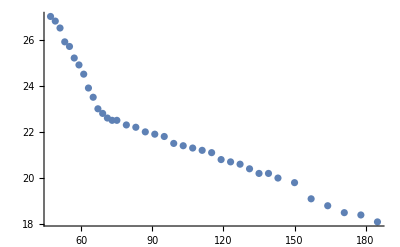

```mathematica
ListPlot[data]
```

```mathematica
plotlist = Table[{27-data[[i,2]],data[[i,1]]*0.89+6},{i,1,Length[data]}]
```

{{0,47.83},{0.2,49.61},{0.5,51.39},{1.1,53.17},{1.3,54.95},{1.8,56.73},{2.1,58.51},{2.5,60.29},{3.1,62.07},{3.5,63.85},{4.,65.63},{4.2,67.41},{4.4,69.19},{4.5,70.97},{4.5,72.75},{4.7,76.31},{4.8,79.87},{5.,83.43},{5.1,86.99},{5.2,90.55},{5.5,94.11},{5.6,97.67},{5.7,101.23},{5.8,104.79},{5.9,108.35},{6.2,111.91},{6.3,115.47},{6.4,119.03},{6.6,122.59},{6.8,126.15},{6.8,129.71},{7.,133.27},{7.2,139.5},{7.9,145.73},{8.2,151.96},{8.5,158.19},{8.6,164.42},{8.9,170.65}}

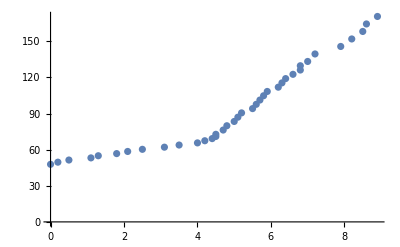

```mathematica
ListPlot[plotlist]
```

```mathematica
list1 = plotlist[[1;;11]]
```

{{0,47.83},{0.2,49.61},{0.5,51.39},{1.1,53.17},{1.3,54.95},{1.8,56.73},{2.1,58.51},{2.5,60.29},{3.1,62.07},{3.5,63.85},{4.,65.63}}

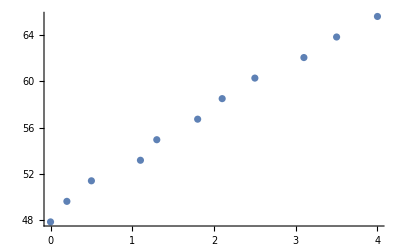

```mathematica
ListPlot[list1]
```

```mathematica
lm1 = LinearModelFit[list1,x,x]
```

FittedModel[48.769+4.35676 x]

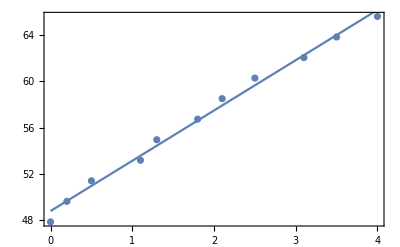

```mathematica
plot1 =Show[ListPlot[list1],Plot[lm1[x],{x,0,4}],Frame -> True]
```

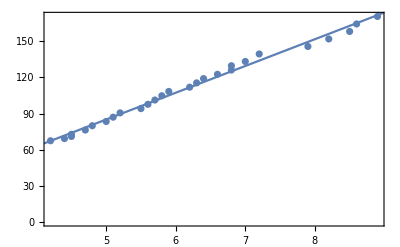

```mathematica
list2  = plotlist[[12;;]];
lm2 = LinearModelFit[list2,x,x];
plot2 = Show[ListPlot[list2],Plot[lm2[x],{x,4,9}],Frame-> True]
```

```mathematica
lm2
```

FittedModel[-26.0706+22.2255 x]

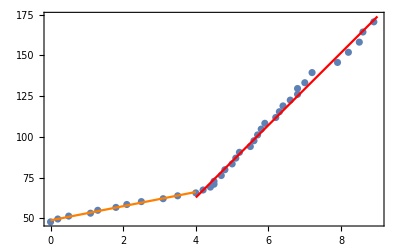

```mathematica
Show[ListPlot[plotlist],Plot[lm1[x],{x,0,4},PlotStyle->Orange],Plot[lm2[x],{x,4,9},PlotStyle->Red],Frame-> True,PlotRange-> All]
```

```mathematica
hwasser = 30-18.1
```

11.9

```mathematica
hwasser Pi 2.3^2
```

197.766

```mathematica
Needs["ErrorBarPlots`"]
```

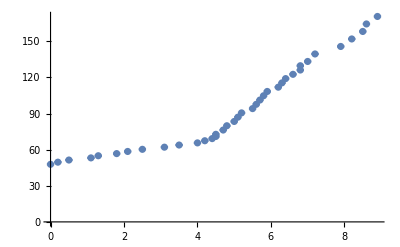

```mathematica
errorplot = Table[{{plotlist[[i,1]],plotlist[[i,2]]},ErrorBar[0.1,0.9]},{i,1,Length[plotlist]}];
ErrorListPlot[errorplot]
```

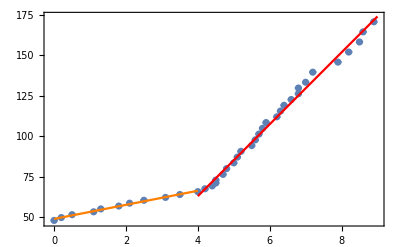

```mathematica
Show[ErrorListPlot[errorplot],Plot[lm1[x],{x,0,4},PlotStyle->Orange],Plot[lm2[x],{x,4,9},PlotStyle->Red],Frame-> True,PlotRange-> All]
```